```mathematica
ψ[z_] = z Tanh[ π/2 Sinh[z]];
exp[z_] = (-2 π I z)/h+Log[π/h Sqrt[ψ[z]]]+Log[π/h ψ'[z]]- (ψ[z]^2 π^2)/(4 σ^2 h^2)- I π/h ψ[z];
```

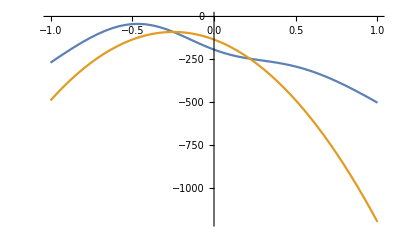

```mathematica
Plot[{Re[exp[x-I π/10]/.h-> 0.01/.σ-> 10],Re[approx/.h-> 0.01/.σ-> 1]}, {x,-1,1}]
```

```mathematica
approx = Normal@Series[exp[x-I π/10],{x,0,8}];
```

```mathematica
NIntegrate[Exp[approx/.h-> 0.4/.σ-> 1],{x,-Infinity,Infinity}]
```

0.00336557+0.00429817 ⅈ

```mathematica
Plot[NIntegrate[Exp[approx/.σ-> 1],{x,-Infinity,Infinity}],{h,0.01,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

$Aborted

```mathematica
hlist = {0.05,0.1,0.15,0.2,0.25,0.3,0.4,0.5};
int= {};
For[i=1, i≤ Length[hlist],i++, AppendTo[int,Abs[NIntegrate[Exp[approx/.σ-> 1/.h-> hlist[[i]]],{x,-Infinity,Infinity}]]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.367698}. NIntegrate obtained -16871.+1460. ⅈ and 246978. for the integral and error estimates.

```mathematica
int
```

{16934.1,0.000279413,0.00149904,0.00275299,0.00428229,0.00604065,0.00545907,0.0278615}

```mathematica
For[i=1, i++, i≤ Length[hlist], Print[i]]
For[i=0,i<4,i++,Print[i]]
```

```mathematica
Length[hlist]
```

5

```mathematica
ψ[z_] = z Tanh[ π/2 Sinh[z]];
exp[z_] = (-2 π I z)/h+Log[π/h Sqrt[ψ[z]]]+Log[π/h ψ'[z]]- (ψ[z] π)/(σ h)- I π/h ψ[z];
approx = Normal@Series[exp[x-I π/7],{x,-0.25,2}];
```

```mathematica
hlist = {0.05,0.1,0.15,0.2,0.25,0.3,0.4,0.5};
int= {};
For[i=1, i≤ Length[hlist],i++, AppendTo[int,Abs[NIntegrate[Exp[approx/.σ-> 1/.h-> hlist[[i]]],{x,-Infinity,Infinity}]]]]
int
```

{1.86176×10^-7,0.00294334,0.0562347,0.213313,0.434999,0.659383,0.996474,1.16446}

{1.79682×10^-7,4.94141×10^-6,0.000417143,0.00351394,0.0119852,0.0262481,0.0659312,0.108985}

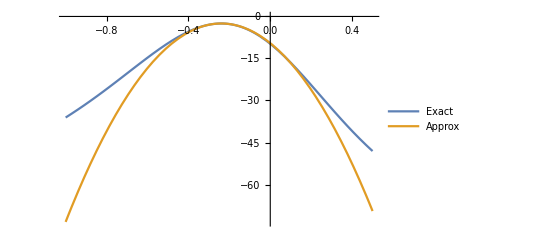

```mathematica
Plot[{Re[exp[x-I π/7]/.h-> 0.1/.σ-> 1],Re[approx/.h-> 0.1/.σ-> 1]}, {x,-1,0.5}, PlotLegends->{"Exact","Approx"}]
```

```mathematica
a = Collect[approx,x]/.x-> 0/.σ-> λ;
b = D[Collect[approx,x],x]/.x-> 0/.σ-> λ;
c = D[Collect[approx,x],{x,2}]/.x-> 0/.σ-> λ;
inv[h_,λ_] = (ⅇ^(-a+b^2/(4 c)))/(√2 √c)
```

((0.00874761+0.0550714 ⅈ) ⅇ^((1.51227-2.11604 ⅈ)/h-0.0625 ((0.00793712+3.90024 ⅈ)-(6.17768+6.06726 ⅈ)/h-(6.06726-6.17768 ⅈ)/(h λ))-(0.545245-1.30762 ⅈ)/(h λ)+((0.204334-1.21805 ⅈ) ((0.665944-1.01825 ⅈ)-(0.236052-0.876358 ⅈ) λ+(1.+0. ⅈ) h λ))/(h λ)+(0.5 ((0.00793712+3.90024 ⅈ)-(6.17768+6.06726 ⅈ)/h-(6.06726-6.17768 ⅈ)/(h λ))-((0.817335-4.87221 ⅈ) ((0.665944-1.01825 ⅈ)-(0.236052-0.876358 ⅈ) λ+(1.+0. ⅈ) h λ))/(h λ))^2/(4 ((0.+0. ⅈ)+2 ((0.00793712+3.90024 ⅈ)-(6.17768+6.06726 ⅈ)/h-(6.06726-6.17768 ⅈ)/(h λ))))) h^2)/(√((0.+0. ⅈ)+2 ((0.00793712+3.90024 ⅈ)-(6.17768+6.06726 ⅈ)/h-(6.06726-6.17768 ⅈ)/(h λ))))

```mathematica
Numerator[%162]
```

(0.00874761+0.0550714 ⅈ) ⅇ^((1.89838+0.379204 ⅈ)/h+(0.379204+1.30762 ⅈ)/(h λ)+(0.204334 ((0.665944-1.01825 ⅈ)-(0.236052-0.876358 ⅈ) λ+1. h λ))/(h λ)+(0.5 ((0.00793712+3.90024 ⅈ)-(6.17768+6.06726 ⅈ)/h-(6.06726-6.17768 ⅈ)/(h λ))-((0.817335-4.87221 ⅈ) ((0.665944-1.01825 ⅈ)-(0.236052-0.876358 ⅈ) λ+1. h λ))/(h λ))^2/(8 ((0.00793712+3.90024 ⅈ)-(6.17768+6.06726 ⅈ)/h-(6.06726-6.17768 ⅈ)/(h λ)))) h^2

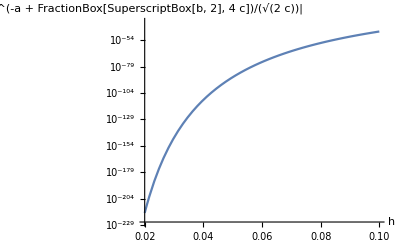

```mathematica
LogPlot[Abs[inv[h,λ]/(λ/((1+λ^2)^(3/2)))/.λ-> 0.05], {h,0.02,0.1}, AxesLabel->{"h", "|e^(-a + FractionBox[SuperscriptBox[b, 2], 4 c])/(√(2 c))|"}]
```

```mathematica
Integrate[Exp[approx],{x,-Infinity,Infinity}, Assumptions->{h>0,σ>0}]
```

$Aborted

```mathematica
Sqrt[2 d]
```

√2 √d

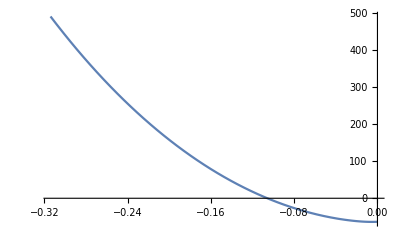

```mathematica
Plot[Im[exp[0.01+I y]]/.h-> 0.001/.σ-> 1, {y,-π/10,0}]
```

```mathematica
Integrate[Exp[approx],{x,-Infinity,Infinity}]
```

$Aborted

```mathematica
Simplify[ComplexExpand[approx], Assumptions->{h>0,σ>0}]
```

$Aborted

```mathematica
approx0 = Normal@SeriesCoefficient[exp[x-I π/10],{x,0,0}];
approx1 = Normal@SeriesCoefficient[exp[x-I π/10],{x,0,1}]-approx0;
approx2 = Normal@SeriesCoefficient[exp[x-I π/10],{x,0,2}]-approx1;
```

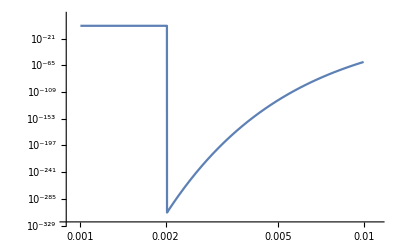

```mathematica
val = Abs[Exp[approx0+approx1/(4 approx2)]Sqrt[π/approx2]];
LogLogPlot[val/.σ-> 1,{h,0.001,0.01}]
```

```mathematica
val/.σ-> 1/.h-> 0.01
```

(2.96562×10^-6)/(√Abs[(0.+0. ⅈ)+(516.17-495.4 ⅈ) x^2])

```mathematica
Integrate[Exp[-a-b x- c x^2],{x,-Infinity,Infinity}, Assumptions->{a>0,b>0,c>0}]
```

(ⅇ^(-a+b^2/(4 c)) √π)/(√c)

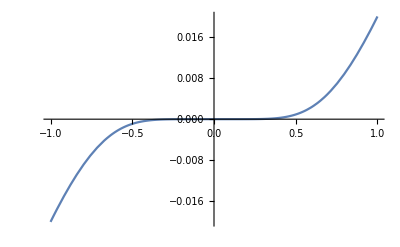

```mathematica
Plot[BesselJ[3,ψ[x]]ψ'[x],{x,-1,1}]
```

```mathematica
ψ[10+I π/3]//N
ψ[10-I π/3]//N
```

10.+1.0472 ⅈ

10.-1.0472 ⅈ

```mathematica
ψ'[1+I π/3]//N
ψ'[-1-I π/3]//N
```

-0.839074-1.09466 ⅈ

0.839074+1.09466 ⅈ

```mathematica
ψ[10+I π/3]//N
ψ[-10+I π/3]//N
```

10.+1.0472 ⅈ

10.-1.0472 ⅈ

```mathematica
1/Sqrt[2 π] Integrate[Exp[-a-b x-c x^2],{x,-Infinity,Infinity}, Assumptions->{a>0,b>0,c>0}]
```

(ⅇ^(-a+b^2/(4 c)))/(√2 √c)

```mathematica
TeXForm[%187]
```

\frac{e^{\frac{b^2}{4 c}-a}}{\sqrt{2} \sqrt{c}}

```mathematica
Integrate[x Exp[- λ x]BesselJ[0,x], {x,0,Infinity}, Assumptions->{λ>0}]
```

λ/((1+λ^2)^(3/2))

```mathematica
Integrate[x Exp[- λ x]BesselJ[0,x], {x,R,Infinity}, Assumptions->{λ>0,R>0}]
```

Integrate[ⅇ^(-x λ) x BesselJ[0,x],{x,R,∞},Assumptions→{λ>0,R>0}]

```mathematica
Simplify[Integrate[x Exp[-λ x-I x Sin[τ]],{x,R,Infinity}], Assumptions->{λ>0,τ>0}]
```

(ⅇ^(-R (λ+ⅈ Sin[τ])) (1+R λ+ⅈ R Sin[τ]))/(λ+ⅈ Sin[τ])^2

```mathematica
Simplify[Abs[ComplexExpand[%196]], Assumptions->{R>0,λ>0,τ>0}]
```

ⅇ^(-R λ) Abs[((1+R λ+ⅈ R Sin[τ]) (Cos[R Sin[τ]]-ⅈ Sin[R Sin[τ]]))/(λ+ⅈ Sin[τ])^2]

```mathematica
Integrate[Sqrt[(1+R λ)^2+R^2 Sin[τ]^2]/(λ^2+Sin[τ]^2),{τ,-π,π}, Assumptions->{λ>0,R>0}]
```

$Aborted

```mathematica
Integrate[ⅇ^(-R (λ+ⅈ Sin[τ]))/(λ+ⅈ Sin[τ])^2, {τ,-π,π}, Assumptions->{λ>0,R>0}]
```

$Aborted

```mathematica
Integrate[R ⅇ^(-R (λ + I Sin[τ]))/(λ+ I Sin[τ]), {τ,-π,π}, Assumptions->{λ>0,R>0}]
```

$Aborted

```mathematica
222
```

```mathematica
Solve[a x^2+b x+c == 0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
D[a x^2+b x+c, x]
```

b+2 a x

```mathematica
ψ[10+I π/3]//N
ψ[-10-I π/3]//N
```

10.+1.0472 ⅈ

10.+1.0472 ⅈ

```mathematica
ψ'[1+I π/3]//N
ψ'[-1-I π/3]//N
```

-0.839074-1.09466 ⅈ

0.839074+1.09466 ⅈ

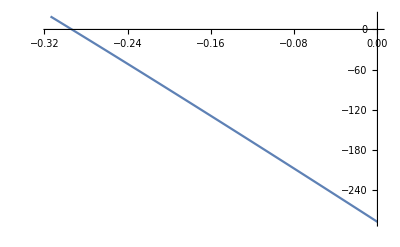

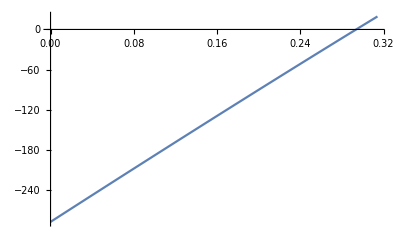

```mathematica
Plot[{Re[exp[1-I y]/.h-> 0.01/.σ-> 1]}, {y,-π/10,0}]
Plot[{Re[exp[1+I y]/.h-> 0.01/.σ-> 1]}, {y,0,π/10}]
```

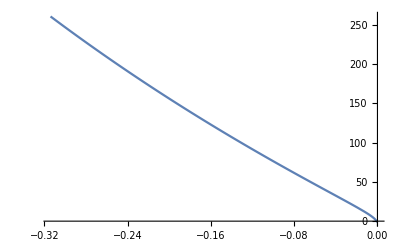

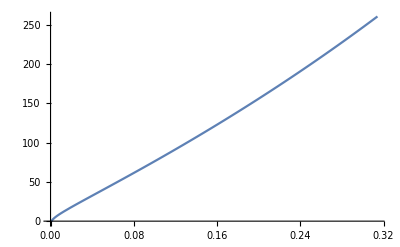

```mathematica
Plot[{Re[exp[0.001-I y]/.h-> 0.01/.σ-> 1]}, {y,-π/10,0}]
Plot[{Re[exp[0.001+I y]/.h-> 0.01/.σ-> 1]}, {y,0,π/10}]
```

```mathematica
Integrate[exp[x+I y],{y,0,π/10}]
```

$Aborted

```mathematica
Normal@Series[exp[x+I y], {y,0,2}]
```

-(2 ⅈ π x)/h+Log[(π √(x Tanh[1/2 π Sinh[x]]))/h]+Log[(π (1/2 π x Cosh[x] Sech[1/2 π Sinh[x]]^2+Tanh[1/2 π Sinh[x]]))/h]-(ⅈ π x Tanh[1/2 π Sinh[x]])/h-(π x Tanh[1/2 π Sinh[x]])/(h σ)+y ((2 π)/h+ⅈ/(2 x)+1/4 ⅈ π Cosh[x] Coth[1/2 π Sinh[x]]-1/4 ⅈ π Cosh[x] Tanh[1/2 π Sinh[x]]-(ⅈ π (-Cosh[x]-Cosh[x] Sech[1/2 π Sinh[x]]^2-x Sech[1/2 π Sinh[x]]^2 Sinh[x]+π x Cosh[x]^2 Sech[1/2 π Sinh[x]]^2 Tanh[1/2 π Sinh[x]]+Cosh[x] Tanh[1/2 π Sinh[x]]^2))/(π x Cosh[x] Sech[1/2 π Sinh[x]]^2+2 Tanh[1/2 π Sinh[x]])+(ⅈ π (-π x Cosh[x]-2 Tanh[1/2 π Sinh[x]]+π x Cosh[x] Tanh[1/2 π Sinh[x]]^2))/(2 h σ)+(π^2 x Cosh[x]+2 π Tanh[1/2 π Sinh[x]]-π^2 x Cosh[x] Tanh[1/2 π Sinh[x]]^2)/(2 h))+y^2 (1/(16 x^2)(-π^2 x^2 Cosh[x]^2+4 Coth[1/2 π Sinh[x]]^2+π^2 x^2 Cosh[x]^2 Coth[1/2 π Sinh[x]]^4+2 π x^2 Coth[1/2 π Sinh[x]] Sinh[x]-2 π x^2 Coth[1/2 π Sinh[x]]^3 Sinh[x]) Tanh[1/2 π Sinh[x]]^2+1/(4 h σ)π^2 (2 Cosh[x]+x Sinh[x]-π x Cosh[x]^2 Tanh[1/2 π Sinh[x]]-2 Cosh[x] Tanh[1/2 π Sinh[x]]^2-x Sinh[x] Tanh[1/2 π Sinh[x]]^2+π x Cosh[x]^2 Tanh[1/2 π Sinh[x]]^3)+1/(4 h)ⅈ (2 π^2 Cosh[x]+π^2 x Sinh[x]-π^3 x Cosh[x]^2 Tanh[1/2 π Sinh[x]]-2 π^2 Cosh[x] Tanh[1/2 π Sinh[x]]^2-π^2 x Sinh[x] Tanh[1/2 π Sinh[x]]^2+π^3 x Cosh[x]^2 Tanh[1/2 π Sinh[x]]^3)+1/2 ((π^2 (-Cosh[x]-Cosh[x] Sech[1/2 π Sinh[x]]^2-x Sech[1/2 π Sinh[x]]^2 Sinh[x]+π x Cosh[x]^2 Sech[1/2 π Sinh[x]]^2 Tanh[1/2 π Sinh[x]]+Cosh[x] Tanh[1/2 π Sinh[x]]^2)^2)/(4 (1/2 π x Cosh[x] Sech[1/2 π Sinh[x]]^2+Tanh[1/2 π Sinh[x]])^2)-(π (2 x Cosh[x] Sech[1/2 π Sinh[x]]^2-π^2 x Cosh[x]^3 Sech[1/2 π Sinh[x]]^2+2 Sinh[x]+4 Sech[1/2 π Sinh[x]]^2 Sinh[x]-2 π Cosh[x]^2 Tanh[1/2 π Sinh[x]]-4 π Cosh[x]^2 Sech[1/2 π Sinh[x]]^2 Tanh[1/2 π Sinh[x]]-6 π x Cosh[x] Sech[1/2 π Sinh[x]]^2 Sinh[x] Tanh[1/2 π Sinh[x]]+3 π^2 x Cosh[x]^3 Sech[1/2 π Sinh[x]]^2 Tanh[1/2 π Sinh[x]]^2-2 Sinh[x] Tanh[1/2 π Sinh[x]]^2+2 π Cosh[x]^2 Tanh[1/2 π Sinh[x]]^3))/(4 (1/2 π x Cosh[x] Sech[1/2 π Sinh[x]]^2+Tanh[1/2 π Sinh[x]]))))

```mathematica
Integrate[Exp[%58],{y,0,π/7}]
```

$Aborted

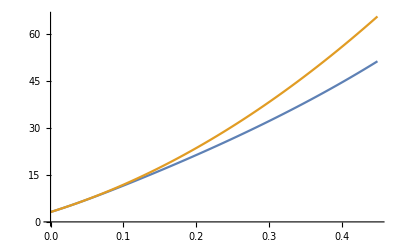

```mathematica
Plot[{Re[exp[0.1+I y]/.h-> 0.1/.σ-> 1],Re[%58/.h-> 0.1/.σ-> 1/.x-> 0.1]}, {y,0,π/7}]
```

```mathematica
1/Sqrt[2 π] Integrate[Exp[-a-b x-c x^2],{x,-Infinity,Infinity}, Assumptions->{a>0,b>0,c>0}]
```

(ⅇ^(-a+b^2/(4 c)))/(√2 √c)

```mathematica
Simplify[%,Assumptions->{a>0,b>0,c>0}]
```

(ⅇ^(-a+b^2/(4 c)))/(√2 √c)

```mathematica
Simplify[Integrate[-I(π/h)^2 x Sqrt[2/(π π/h x)]Cos[π/h x-π/4]Exp[- π/h λ x-2 π/h I (x+I yp) ], {yp,-y,0}, Assumptions->{y>0,x>0,h>0,λ>0}]+Integrate[I(π/h)^2 x Sqrt[2/(π π/h x)]Cos[π/h x-π/4]Exp[- π/h λ x+2 π/h I (x+I yp) ], {yp,0,y}, Assumptions->{y>0,x>0,h>0,λ>0}]+Integrate[-I(π/h)^2 x Sqrt[2/(π π/h x)]Cos[π/h x-π/4]Exp[- π/h λ x+2 π/h I (-x+I yp) ] , {yp,y,0}, Assumptions->{y>0,x>0,h>0,λ>0}]+Integrate[I(π/h)^2 x Sqrt[2/(π π/h x)]Cos[π/h x-π/4]Exp[- π/h λ x-2 π/h I (-x+I yp) ], {yp,0,-y}, Assumptions->{y>0,x>0,h>0,λ>0}], Assumptions->{y>0,x>0,h>0,λ>0}]
```

0

```mathematica
ψ[10+I π/3]//N
ψ[-10-I π/3]//N
ψ'[0.1+I π/3]//N
ψ'[-0.1-I π/3]//N
```

10.+1.0472 ⅈ

10.+1.0472 ⅈ

12.5163+18.4372 ⅈ

-12.5163-18.4372 ⅈ

```mathematica
Simplify[ComplexExpand[Integrate[(π/h)^2 x Sqrt[2/(π π/h x)]Cos[π/h x-π/4]Exp[- π/h λ x ], {x,R,Infinity}, Assumptions->{λ>0,h>0,R>0}]], Assumptions->{h>0,R>0,λ>0}]
```

1/(4 √h (1+λ^2)^(9/4))ⅇ^(-(π R λ)/h) ((Cos[1/4 (Arg[-ⅈ+λ]+Arg[ⅈ+λ])]-ⅈ Sin[1/4 (Arg[-ⅈ+λ]+Arg[ⅈ+λ])]) (ⅇ^((π R λ)/h) (ⅈ+λ)^2 Re[Erf[√π ((R^2 (1+λ^2))/h^2)^(1/4) (Cos[1/2 Arg[-ⅈ+λ]]+ⅈ Sin[1/2 Arg[-ⅈ+λ]])]] ((√h (-ⅈ+λ)+ⅈ √(h (1+λ^2))) Cos[1/2 Arg[-ⅈ+λ]]-(√h (1+ⅈ λ)+√(h (1+λ^2))) Sin[1/2 Arg[-ⅈ+λ]]) (ⅈ Cos[1/4 Arg[(-ⅈ+λ)^2 (ⅈ+λ)]]+Sin[1/4 Arg[(-ⅈ+λ)^2 (ⅈ+λ)]])+ⅇ^((π R λ)/h) (-ⅈ+λ)^2 Im[Erf[√π ((R^2 (1+λ^2))/h^2)^(1/4) (Cos[1/2 Arg[ⅈ+λ]]+ⅈ Sin[1/2 Arg[ⅈ+λ]])]] (√(h (1+λ^2)) Cos[1/4 (2 Arg[ⅈ+λ]-Arg[(-ⅈ+λ)^2 (ⅈ+λ)])]+√h (1-ⅈ λ) Cos[1/4 Arg[(-ⅈ+λ)^2 (ⅈ+λ)]]+ⅈ √(h (1+λ^2)) Sin[1/4 (2 Arg[ⅈ+λ]-Arg[(-ⅈ+λ)^2 (ⅈ+λ)])]+ⅈ √h Sin[1/4 Arg[(-ⅈ+λ)^2 (ⅈ+λ)]]+√h λ Sin[1/4 Arg[(-ⅈ+λ)^2 (ⅈ+λ)]])-(-ⅈ+λ) (-2 (ⅈ+λ) (2 (1+λ) (R^2 (1+λ^2))^(1/4) Cos[(π R)/h]+ⅇ^((π R λ)/h) √(h (1+λ^2)) Cos[3/4 (Arg[-ⅈ+λ]-Arg[ⅈ+λ])]-2 (R^2 (1+λ^2))^(1/4) Sin[(π R)/h]+2 λ (R^2 (1+λ^2))^(1/4) Sin[(π R)/h]-ⅇ^((π R λ)/h) √(h (1+λ^2)) Sin[3/4 (Arg[-ⅈ+λ]-Arg[ⅈ+λ])]) (Cos[1/4 Arg[(-ⅈ+λ)^2 (ⅈ+λ)]]-ⅈ Sin[1/4 Arg[(-ⅈ+λ)^2 (ⅈ+λ)]])+ⅇ^((π R λ)/h) (1+ⅈ λ) Re[Erf[√π ((R^2 (1+λ^2))/h^2)^(1/4) (Cos[1/2 Arg[ⅈ+λ]]+ⅈ Sin[1/2 Arg[ⅈ+λ]])]] (√(h (1+λ^2)) Cos[1/4 (2 Arg[ⅈ+λ]-Arg[(-ⅈ+λ)^2 (ⅈ+λ)])]+√h (1-ⅈ λ) Cos[1/4 Arg[(-ⅈ+λ)^2 (ⅈ+λ)]]+ⅈ √(h (1+λ^2)) Sin[1/4 (2 Arg[ⅈ+λ]-Arg[(-ⅈ+λ)^2 (ⅈ+λ)])]+ⅈ √h Sin[1/4 Arg[(-ⅈ+λ)^2 (ⅈ+λ)]]+√h λ Sin[1/4 Arg[(-ⅈ+λ)^2 (ⅈ+λ)]])))+ⅇ^((π R λ)/h) (ⅈ+λ)^2 Im[Erf[√π ((R^2 (1+λ^2))/h^2)^(1/4) (Cos[1/2 Arg[-ⅈ+λ]]+ⅈ Sin[1/2 Arg[-ⅈ+λ]])]] (-ⅈ (√h (-1-ⅈ λ)+√(h (1+λ^2))) Cos[1/2 Arg[-ⅈ+λ]]+(√h (1+ⅈ λ)+√(h (1+λ^2))) Sin[1/2 Arg[-ⅈ+λ]]) (Cos[1/4 (Arg[-ⅈ+λ]+Arg[ⅈ+λ]+Arg[(-ⅈ+λ)^2 (ⅈ+λ)])]-ⅈ Sin[1/4 (Arg[-ⅈ+λ]+Arg[ⅈ+λ]+Arg[(-ⅈ+λ)^2 (ⅈ+λ)])])) (Cos[1/4 (-Arg[-ⅈ+λ]-Arg[ⅈ+λ]-Arg[(-ⅈ+λ)^2 (ⅈ+λ)])]+ⅈ Sin[1/4 (Arg[-ⅈ+λ]+Arg[ⅈ+λ]+Arg[(-ⅈ+λ)^2 (ⅈ+λ)])])

```mathematica
Integrate[(π/h)^2 x Sqrt[2/(π π/h x)]Cos[π/h x-π/4]Exp[- π/h λ x ], {x,h n,Infinity}, Assumptions->{λ>0,h>0,n>0}]
```

1/4 ((2 Cos[3/2 ArcTan[1/λ]])/((1+λ^2)^(3/4))-1/((-1-ⅈ λ) √(-ⅈ+λ) (ⅈ+λ)^2)ⅇ^(-2 n π λ) (-ⅇ^(2 n π λ) (ⅈ+λ)^2 Erf[√π √(n (-ⅈ+λ))]+√(-ⅈ+λ) (-2 ⅇ^(n π (-ⅈ+λ)) √n (ⅈ+λ) (-ⅈ+λ-ⅇ^(2 ⅈ n π) (ⅈ+λ))+ⅇ^(2 n π λ) (-ⅈ+λ) √(ⅈ+λ) Erf[√π √(n (ⅈ+λ))]))+1/((1+λ^2)^2)ⅇ^(-2 n π λ) (-ⅇ^(2 n π λ) √(-ⅈ+λ) (ⅈ+λ)^2 Erf[√π √(n (-ⅈ+λ))]+ⅇ^(n π (-ⅈ+λ)) (-ⅈ+λ) (2 √n (ⅈ+λ) (-ⅈ+λ+ⅇ^(2 ⅈ n π) (ⅈ+λ))-ⅇ^(n π (ⅈ+λ)) √((-ⅈ+λ)^2 (ⅈ+λ)) Erf[√π √(n (ⅈ+λ))]))+(2 Sin[3/2 ArcTan[1/λ]])/((1+λ^2)^(3/4)))

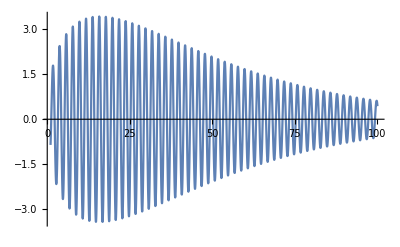

```mathematica
Plot[%84/.R-> h n/.h-> 0.1/.λ-> 0.01, {n, 1,100}]
```

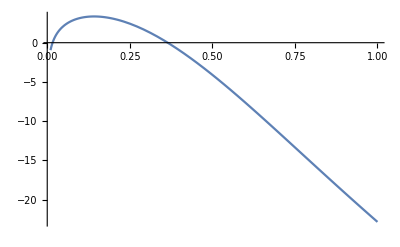

```mathematica
Plot[Re[exp[x]]/.h-> 0.1/.σ-> 1, {x,0.01,1}]
```

```mathematica
Integrate[(π/h)^2 ψ[x]ψ'[x]Sqrt[2/(π π/h ψ[x])]Cos[π/h ψ[x]-π/4]Exp[- π/h λ ψ[x] ],{x,R,Infinity}, Assumptions->{R>0,h>0,λ>0}]
```

$Aborted

```mathematica
Integrate[(π/h)^2 x Sqrt[2/(π π/h x)]Cos[π/h x-π/4]Exp[- π/h λ x ], {x,R,Infinity}, Assumptions->{λ>0,h>0,R>0}]
```

1/(4 √h)(-1/((-1-ⅈ λ) √(-ⅈ+λ) (ⅈ+λ)^2)ⅇ^(-(2 π R λ)/h) h (-(ⅇ^((2 π R λ)/h) (ⅈ+λ)^2 Erf[√π √((R (-ⅈ+λ))/h)])/(√h)+(√(R (-ⅈ+λ)) (-2 ⅇ^((π R (-ⅈ+λ))/h) (ⅈ+λ) (-ⅈ+λ-ⅇ^((2 ⅈ π R)/h) (ⅈ+λ))+ⅇ^((2 π R λ)/h) (-ⅈ+λ) √((h (ⅈ+λ))/R) Erf[√π √((R (ⅈ+λ))/h)]))/h)+1/((1+λ^2)^(11/4))ⅇ^(-(2 π R λ)/h) (-ⅇ^((2 π R λ)/h) √(h (-ⅈ+λ)) (ⅈ+λ)^2 (1+λ^2)^(3/4) Erf[√π √((R (-ⅈ+λ))/h)]+ⅇ^((π R (-ⅈ+λ))/h) (-ⅈ+λ) (2 (ⅈ+λ) (√R (1+λ^2)^(3/4) (-ⅈ+λ+ⅇ^((2 ⅈ π R)/h) (ⅈ+λ))+ⅇ^((π R (ⅈ+λ))/h) √h (1+λ^2) Cos[3/2 ArcTan[1/λ]])-ⅇ^((π R (ⅈ+λ))/h) √(h (-ⅈ+λ)^2 (ⅈ+λ)) (1+λ^2)^(3/4) Erf[√π √((R (ⅈ+λ))/h)]))+(2 √h Sin[3/2 ArcTan[1/λ]])/((1+λ^2)^(3/4)))

```mathematica
%106/.R-> ψ[R]/.R-> h n
```

1/(4 √h)((2 √h Sin[3/2 ArcTan[1/λ]])/((1+λ^2)^(3/4))-1/((-1-ⅈ λ) √(-ⅈ+λ) (ⅈ+λ)^2)ⅇ^(-2 n π λ Tanh[1/2 π Sinh[h n]]) h (-(ⅇ^(2 n π λ Tanh[1/2 π Sinh[h n]]) (ⅈ+λ)^2 Erf[√π √(n (-ⅈ+λ) Tanh[1/2 π Sinh[h n]])])/(√h)+1/h(-2 ⅇ^(n π (-ⅈ+λ) Tanh[1/2 π Sinh[h n]]) (ⅈ+λ) (-ⅈ+λ-ⅇ^(2 ⅈ n π Tanh[1/2 π Sinh[h n]]) (ⅈ+λ))+ⅇ^(2 n π λ Tanh[1/2 π Sinh[h n]]) (-ⅈ+λ) √(((ⅈ+λ) Coth[1/2 π Sinh[h n]])/n) Erf[√π √(n (ⅈ+λ) Tanh[1/2 π Sinh[h n]])]) √(h n (-ⅈ+λ) Tanh[1/2 π Sinh[h n]]))+1/((1+λ^2)^(11/4))ⅇ^(-2 n π λ Tanh[1/2 π Sinh[h n]]) (-ⅇ^(2 n π λ Tanh[1/2 π Sinh[h n]]) √(h (-ⅈ+λ)) (ⅈ+λ)^2 (1+λ^2)^(3/4) Erf[√π √(n (-ⅈ+λ) Tanh[1/2 π Sinh[h n]])]+ⅇ^(n π (-ⅈ+λ) Tanh[1/2 π Sinh[h n]]) (-ⅈ+λ) (-ⅇ^(n π (ⅈ+λ) Tanh[1/2 π Sinh[h n]]) √(h (-ⅈ+λ)^2 (ⅈ+λ)) (1+λ^2)^(3/4) Erf[√π √(n (ⅈ+λ) Tanh[1/2 π Sinh[h n]])]+2 (ⅈ+λ) (ⅇ^(n π (ⅈ+λ) Tanh[1/2 π Sinh[h n]]) √h (1+λ^2) Cos[3/2 ArcTan[1/λ]]+(1+λ^2)^(3/4) (-ⅈ+λ+ⅇ^(2 ⅈ n π Tanh[1/2 π Sinh[h n]]) (ⅈ+λ)) √(h n Tanh[1/2 π Sinh[h n]])))))

```mathematica
1/(4 √h)((2 √h Sin[3/2 ArcTan[1/λ]])/((1+λ^2)^(3/4))-1/((-1-ⅈ λ) √(-ⅈ+λ) (ⅈ+λ)^2)ⅇ^(-2 n π λ Tanh[1/2 π Sinh[h n]]) h (-(ⅇ^(2 n π λ Tanh[1/2 π Sinh[h n]]) (ⅈ+λ)^2 Erf[√π √(n (-ⅈ+λ) Tanh[1/2 π Sinh[h n]])])/(√h)+1/h(-2 ⅇ^(n π (-ⅈ+λ) Tanh[1/2 π Sinh[h n]]) (ⅈ+λ) (-ⅈ+λ-ⅇ^(2 ⅈ n π Tanh[1/2 π Sinh[h n]]) (ⅈ+λ))+ⅇ^(2 n π λ Tanh[1/2 π Sinh[h n]]) (-ⅈ+λ) √(((ⅈ+λ) Coth[1/2 π Sinh[h n]])/n) Erf[√π √(n (ⅈ+λ) Tanh[1/2 π Sinh[h n]])]) √(h n (-ⅈ+λ) Tanh[1/2 π Sinh[h n]]))+1/((1+λ^2)^(11/4))ⅇ^(-2 n π λ Tanh[1/2 π Sinh[h n]]) (-ⅇ^(2 n π λ Tanh[1/2 π Sinh[h n]]) √(h (-ⅈ+λ)) (ⅈ+λ)^2 (1+λ^2)^(3/4) Erf[√π √(n (-ⅈ+λ) Tanh[1/2 π Sinh[h n]])]+ⅇ^(n π (-ⅈ+λ) Tanh[1/2 π Sinh[h n]]) (-ⅈ+λ) (-ⅇ^(n π (ⅈ+λ) Tanh[1/2 π Sinh[h n]]) √(h (-ⅈ+λ)^2 (ⅈ+λ)) (1+λ^2)^(3/4) Erf[√π √(n (ⅈ+λ) Tanh[1/2 π Sinh[h n]])]+2 (ⅈ+λ) (ⅇ^(n π (ⅈ+λ) Tanh[1/2 π Sinh[h n]]) √h (1+λ^2) Cos[3/2 ArcTan[1/λ]]+(1+λ^2)^(3/4) (-ⅈ+λ+ⅇ^(2 ⅈ n π Tanh[1/2 π Sinh[h n]]) (ⅈ+λ)) √(h n Tanh[1/2 π Sinh[h n]])))))
```

1/(4 √h)((2 √h Sin[3/2 ArcTan[1/λ]])/((1+λ^2)^(3/4))-1/((-1-ⅈ λ) √(-ⅈ+λ) (ⅈ+λ)^2)ⅇ^(-2 n π λ Tanh[1/2 π Sinh[h n]]) h (-(ⅇ^(2 n π λ Tanh[1/2 π Sinh[h n]]) (ⅈ+λ)^2 Erf[√π √(n (-ⅈ+λ) Tanh[1/2 π Sinh[h n]])])/(√h)+1/h(-2 ⅇ^(n π (-ⅈ+λ) Tanh[1/2 π Sinh[h n]]) (ⅈ+λ) (-ⅈ+λ-ⅇ^(2 ⅈ n π Tanh[1/2 π Sinh[h n]]) (ⅈ+λ))+ⅇ^(2 n π λ Tanh[1/2 π Sinh[h n]]) (-ⅈ+λ) √(((ⅈ+λ) Coth[1/2 π Sinh[h n]])/n) Erf[√π √(n (ⅈ+λ) Tanh[1/2 π Sinh[h n]])]) √(h n (-ⅈ+λ) Tanh[1/2 π Sinh[h n]]))+1/((1+λ^2)^(11/4))ⅇ^(-2 n π λ Tanh[1/2 π Sinh[h n]]) (-ⅇ^(2 n π λ Tanh[1/2 π Sinh[h n]]) √(h (-ⅈ+λ)) (ⅈ+λ)^2 (1+λ^2)^(3/4) Erf[√π √(n (-ⅈ+λ) Tanh[1/2 π Sinh[h n]])]+ⅇ^(n π (-ⅈ+λ) Tanh[1/2 π Sinh[h n]]) (-ⅈ+λ) (-ⅇ^(n π (ⅈ+λ) Tanh[1/2 π Sinh[h n]]) √(h (-ⅈ+λ)^2 (ⅈ+λ)) (1+λ^2)^(3/4) Erf[√π √(n (ⅈ+λ) Tanh[1/2 π Sinh[h n]])]+2 (ⅈ+λ) (ⅇ^(n π (ⅈ+λ) Tanh[1/2 π Sinh[h n]]) √h (1+λ^2) Cos[3/2 ArcTan[1/λ]]+(1+λ^2)^(3/4) (-ⅈ+λ+ⅇ^(2 ⅈ n π Tanh[1/2 π Sinh[h n]]) (ⅈ+λ)) √(h n Tanh[1/2 π Sinh[h n]])))))

```mathematica
Plot[{Re[(%1)/(λ/((1+λ^2)^(3/2)))/.h-> 0.01/.λ-> 0.05],Re[(%1)/(λ/((1+λ^2)^(3/2)))/.h-> 0.1/.λ-> 0.05]}, {n, 50,70}, PlotRange->All, AxesLabel->{Style["N",12],Style["I_h/I",12]}, PlotLegends->Placed[{"h=0.01","h=0.1"},Top Right]]
```

Placed::labpos: Right Top is not a valid position for the placement of labels.

-Graphics-

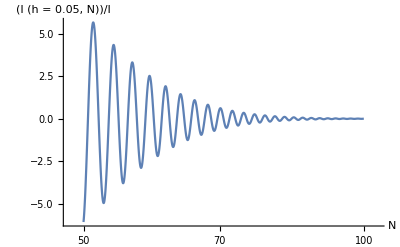

```mathematica
Plot[Re[(%108)/(λ/((1+λ^2)^(3/2)))/.h-> 0.005/.λ-> 0.05], {n, 50,100}, PlotRange->All, AxesLabel->{"N","(I (h = 0.05,  N))/I"}]
```

```mathematica
Integrate[x BesselJ[0,x] Exp[- λ x], {x,0,Infinity}, Assumptions->{λ>0}]
```

λ/((1+λ^2)^(3/2))

```mathematica
I Integrate[(1-Tan[π/h(x+I y)]),{y,-yp,0}, Assumptions->{h>0,x>0,yp>0,Cos[(π x)/h]≥ 0}]
```

ⅈ (yp+(ⅈ h Log[Cos[(π (x-ⅈ yp))/h] Sec[(π x)/h]])/π)

```mathematica
I Integrate[(1+Tan[π/h(x+I y)]),{y,0,yp}, Assumptions->{x>0,h>0,yp>0, Cos[(π x)/h]≥ 0}]
```

ⅈ (yp+(ⅈ h Log[Cos[(π (x+ⅈ yp))/h] Sec[(π x)/h]])/π)

```mathematica
-I Integrate[(1+Tan[π/h(-x+I y)]),{y,yp,0}, Assumptions->{h>0,x>0,yp>0,Cos[(π x)/h]≥ 0}]
```

-ⅈ (-yp-(ⅈ h Log[Cos[(π (x-ⅈ yp))/h] Sec[(π x)/h]])/π)

```mathematica
-I Integrate[(1-Tan[π/h(-x+I y)]),{y,0,-yp}, Assumptions->{h>0,x>0,yp>0,Cos[(π x)/h]≥ 0}]
```

-ⅈ (-yp-(ⅈ h Log[Cos[(π (x+ⅈ yp))/h] Sec[(π x)/h]])/π)

```mathematica
Simplify[%10+%12+%14+%15, Assumptions->{yp>0,h>0,x>0}]
```

(4 ⅈ π yp-2 h Log[Cos[(π (x-ⅈ yp))/h] Sec[(π x)/h]]-2 h Log[Cos[(π (x+ⅈ yp))/h] Sec[(π x)/h]])/π

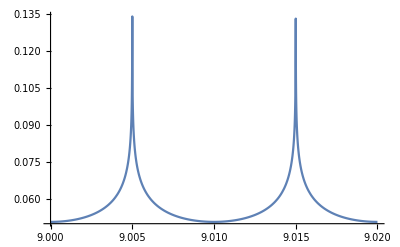

```mathematica
Plot[Abs[%16/.h-> 0.01/.yp-> 0.01],{x,9,9.02}, PlotRange->All]
```

```mathematica
Limit[(4 ⅈ π yp-2 h Log[Cos[(π (x-ⅈ yp))/h] Sec[(π x)/h]]-2 h Log[Cos[(π (x+ⅈ yp))/h] Sec[(π x)/h]])/π, yp-> π/3]
```

(4 ⅈ π^2-6 h (Log[Cosh[(π (π-3 ⅈ x))/(3 h)] Sec[(π x)/h]]+Log[Cosh[(π (π+3 ⅈ x))/(3 h)] Sec[(π x)/h]]))/(3 π)

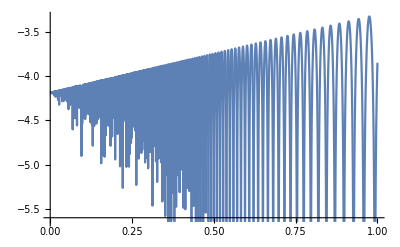

```mathematica
Plot[Re[%1/.x-> 9 π],{h,0.001,1}]
```

```mathematica
Simplify[HankelH1[0,-x], Assumptions->{x>0}]
```

HankelH1[0,-x]

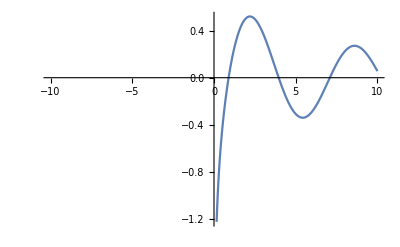

```mathematica
Plot[BesselY[0,x],{x,-10,10}]
```

```mathematica
TrigExpand[Tan[x- π/4]]
```

-Cos[x]/(√2 (Cos[x]/(√2)+Sin[x]/(√2)))+Sin[x]/(√2 (Cos[x]/(√2)+Sin[x]/(√2)))

```mathematica
Integrate[Tan[(π (x+I y))/h- π/4],{y,-z,z}, Assumptions->{h>0,x>0,z>0,Sin[π (1/4+x/h)]≥0}]
```

-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π

```mathematica
Integrate[Tan[(π (x+I y))/h- π/4],{y,-z,z}, Assumptions->{h>0,x>0,z>0,Sin[π (1/4+x/h)]<0}]
```

-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π

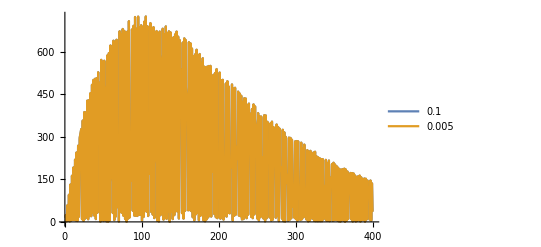

```mathematica
Plot[{Abs[(-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^2 x Exp[- λ/h x])/.λ-> 0.01/.x-> h*n/.h-> 0.1/.z-> π/3],Abs[(-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^2 x Exp[- λ/h x])/.λ-> 0.01/.x-> h*n/.h-> 0.001/.z-> π/3]},{n,1,400}, PlotLegends->{"0.1","0.005"}]
```

```mathematica
Simplify[ComplexExpand[-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π], Assumptions->{x>0,h>0,π/2>z>0}]
```

(h (Arg[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Arg[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π

```mathematica
Plot[Abs[(-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^2 x Exp[- λ/h x])/.λ-> 1/.h-> 0.1/.z-> π/3/.x-> h n],{n,1,100}]
```

-Graphics-

```mathematica
Abs[(-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^2 x Exp[- λ/h x])/.λ-> 1/.x-> h*n/.h-> 0.1/.z-> π/3]
```

ⅇ^(-Re[n]) π Abs[n (Log[Sin[7.85398 ((0.1-4.18879 ⅈ)+0.4 n)]]-Log[Sin[7.85398 ((0.1+4.18879 ⅈ)+0.4 n)]])]

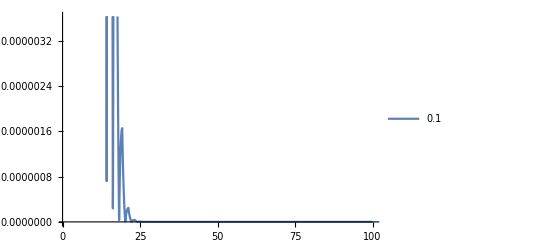

```mathematica
Plot[{Abs[(-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^2 x Exp[- λ/h x])/.λ-> 1/.x-> h*n/.h-> 0.1/.z-> π/4]},{n,1,100}, PlotLegends->{"0.1","0.005"}]
```

```mathematica
Plot[{Abs[(-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^2 x Exp[- λ/h x])/.λ-> 1/.x-> h*n/.h-> 0.0001/.z-> π/3]},{n,1,100}, PlotLegends->{"0.1","0.005"}]
```

-Graphics-

```mathematica
Abs[(-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^2 x Exp[- λ/h x])/.λ-> 1/.x-> h*n/.z-> π/□]
```

ⅇ^(-Re[n]) π Abs[n (Log[Sin[((h+4 h n-(4 ⅈ π)/3) π)/(4 h)]]-Log[Sin[((h+4 h n+(4 ⅈ π)/3) π)/(4 h)]])]

```mathematica
Abs[(-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^2 x Exp[- λ/h x])/.λ-> 1/.x-> h*n/.z-> π/3]
```

ⅇ^(-Re[n]) π Abs[n (Log[Sin[((h+4 h n-(4 ⅈ π)/3) π)/(4 h)]]-Log[Sin[((h+4 h n+(4 ⅈ π)/3) π)/(4 h)]])]

```mathematica
(1/(ⅇ^(-Re[n]) π Abs[n (Log[Sin[78.53981633974483 ((0.01-4.1887902047863905 ⅈ)+0.04 n)]]-Log[Sin[78.53981633974483 ((0.01+4.1887902047863905 ⅈ)+0.04 n)]])]))ⅇ^(-Re[n]) π Abs[n (Log[Sin[7.853981633974483 ((0.1-4.1887902047863905 ⅈ)+0.4 n)]]-Log[Sin[7.853981633974483 ((0.1+4.1887902047863905 ⅈ)+0.4 n)]])]
```

Abs[n (Log[Sin[7.85398 ((0.1-4.18879 ⅈ)+0.4 n)]]-Log[Sin[7.85398 ((0.1+4.18879 ⅈ)+0.4 n)]])]/Abs[n (Log[Sin[78.5398 ((0.01-4.18879 ⅈ)+0.04 n)]]-Log[Sin[78.5398 ((0.01+4.18879 ⅈ)+0.04 n)]])]

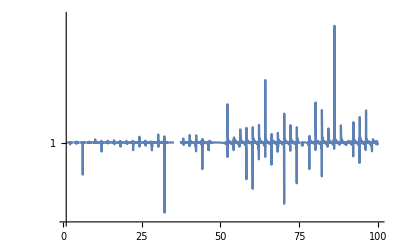

```mathematica
LogPlot[Abs[n (Log[Sin[7.853981633974483 ((0.1-4.1887902047863905 ⅈ)+0.4 n)]]-Log[Sin[7.853981633974483 ((0.1+4.1887902047863905 ⅈ)+0.4 n)]])]/Abs[n (Log[Sin[78.53981633974483 ((0.01-4.1887902047863905 ⅈ)+0.04 n)]]-Log[Sin[78.53981633974483 ((0.01+4.1887902047863905 ⅈ)+0.04 n)]])],{n,1,100}, PlotRange->All]
```

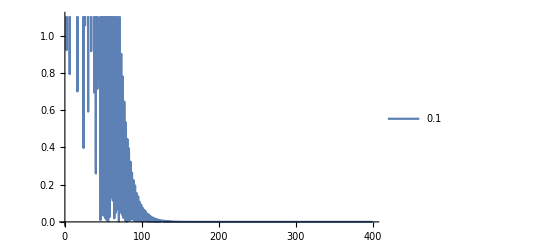

```mathematica
Plot[{Abs[(-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^2 x Exp[- λ/h x])/.λ-> 0.1/.x-> h*n/.h-> 0.1/.z-> π/3]},{n,1,400}, PlotLegends->{"0.1","0.005"}]
```

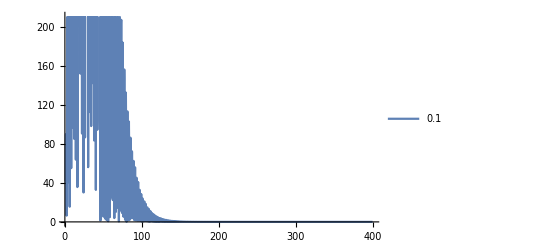

```mathematica
Plot[{Abs[(-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^3 x^2 Exp[- λ/h x])/.λ-> 0.1/.x-> h*n/.h-> 0.01/.z-> π/2]},{n,1,400}, PlotLegends->{"0.1","0.005"}]
```

```mathematica
Series[-ⅈ (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]),{h,0,3}]
```

-ⅈ (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]])

```mathematica
TrigExpand[(Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]/.x-> h n)//Expand]
```

Log[Sin[(π (h+4 h n-4 ⅈ z))/(4 h)]]

```mathematica
Limit[Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]], h-> 0]
```

Limit[Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]],h→0]

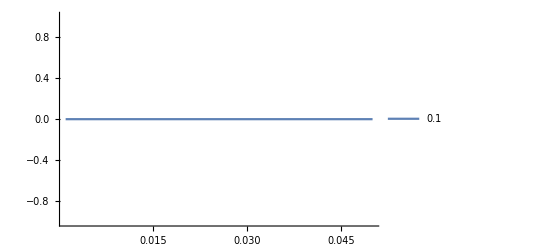

```mathematica
Plot[{Abs[(-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^3 x^2 Exp[- λ/h x])/.λ-> 0.1/.x-> h*n/.z-> π/2/.n-> 200],Abs[(π/□(π/h)^3 x^2 Exp[- λ/h x])/.λ-> 0.1/.x-> h*n/.z-> π/2/.n-> 200]},{h,0.001,0.05}, PlotLegends->{"0.1","0.005"},PlotRange->All]
```

```mathematica
Limit[-(ⅈ h (Log[Sin[(π (h+4 x-4 ⅈ z))/(4 h)]]-Log[Sin[(π (h+4 x+4 ⅈ z))/(4 h)]]))/π(π/h)^3 x^2]
```

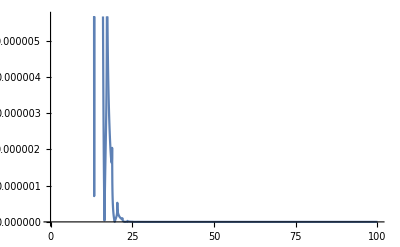

```mathematica
Plot[Abs[-I n π Log[(Sin[π/4+n]-Cos[π/4+n])/(Sin[π/4+n]+Cos[π/4+n])]]Exp[- n],{n,0,100}]
```

```mathematica
Integrate[Tan[(π(h n+I z))/h-π ν/2- π/4], {z,-y,y}, Assumptions->{n>0,h>0,y>0,ν≥ 0, n> 1,2 n- ν>3/2, Sin[1/4 π (1+4 n-2 ν)]≥0}]
```

-(ⅈ h (Log[Cos[(π (h-4 h n+4 ⅈ y+2 h ν))/(4 h)]]-Log[Sin[(π (h+4 h n+4 ⅈ y-2 h ν))/(4 h)]]))/π

```mathematica
Integrate[Tan[(π(h n+I z))/h-π ν/2- π/4], {z,-y,y}, Assumptions->{n>0,h>0,y>0,ν≥ 0, n> 1,2 n- ν>3/2, Sin[1/4 π (1+4 n-2 ν)]< 0}]
```

-(ⅈ h (Log[Cos[(π (h-4 h n+4 ⅈ y+2 h ν))/(4 h)]]-Log[Sin[(π (h+4 h n+4 ⅈ y-2 h ν))/(4 h)]]))/π

```mathematica
TeXForm[-(ⅈ h (Log[Cos[(π (h-4 h n+4 ⅈ y+2 h ν))/(4 h)]]-Log[Sin[(π (h+4 h n+4 ⅈ y-2 h ν))/(4 h)]]))/π]
```

-\frac{i h \left(\log \left(\cos \left(\frac{\pi  (2 h \nu -4 h n+h+4 i y)}{4
   h}\right)\right)-\log \left(\sin \left(\frac{\pi  (-2 h \nu +4 h n+h+4 i y)}{4
   h}\right)\right)\right)}{\pi }

```mathematica
TrigExpand[Cos[(π (h-4 h n+4 ⅈ y+2 h ν))/(4 h)//Expand]]
```

(Cos[n π] Cos[(π ν)/2] Cosh[(π y)/h])/(√2)+(Cos[(π ν)/2] Cosh[(π y)/h] Sin[n π])/(√2)-(Cos[n π] Cosh[(π y)/h] Sin[(π ν)/2])/(√2)+(Cosh[(π y)/h] Sin[n π] Sin[(π ν)/2])/(√2)-(ⅈ Cos[n π] Cos[(π ν)/2] Sinh[(π y)/h])/(√2)+(ⅈ Cos[(π ν)/2] Sin[n π] Sinh[(π y)/h])/(√2)-(ⅈ Cos[n π] Sin[(π ν)/2] Sinh[(π y)/h])/(√2)-(ⅈ Sin[n π] Sin[(π ν)/2] Sinh[(π y)/h])/(√2)

```mathematica
Integrate[Tan[(π(h n+I z))/h- π/4], {z,-y,y}, Assumptions->{R>0,h>0,y>0, Element[n, Integers],n> 2}]
```

Integrate[-Tan[π/4-(π (h n+ⅈ z))/h],{z,-y,y},Assumptions→{R>0,h>0,y>0,n∈Integers,n>2}]

```mathematica
TeXForm[-(ⅈ h (Log[Cos[(π (h-4 h n+4 ⅈ y+2 h ν))/(4 h)]]-Log[Sin[(π (h+4 h n+4 ⅈ y-2 h ν))/(4 h)]]))/π]
```

-\frac{i h \left(\log \left(\cos \left(\frac{\pi  (2 h \nu -4 h n+h+4 i y)}{4
   h}\right)\right)-\log \left(\sin \left(\frac{\pi  (-2 h \nu +4 h n+h+4 i y)}{4
   h}\right)\right)\right)}{\pi }

```mathematica
Integrate[Tan[(π(h n+I z))/h- ν π/2- π/4]/.ν-> 0, {z,-y,y}, Assumptions->{R>0,h>0,y>0, Element[{n,ν}, Integers],n> 1,ν≥ 0}]
```

ConditionalExpression[-(ⅈ h (Log[Sin[π (1/4+n-(ⅈ y)/h)]]-Log[Sin[π (1/4+n+(ⅈ y)/h)]]))/π,Sin[(1/4+n) π]≥0]

```mathematica
(-(ⅈ h (Log[Cos[(π (h-4 h n+4 ⅈ y+2 h ν))/(4 h)]]-Log[Sin[(π (h+4 h n+4 ⅈ y-2 h ν))/(4 h)]]))/π)/.ν-> 0
```

-(ⅈ h (Log[Cos[(π (h-4 h n+4 ⅈ y))/(4 h)]]-Log[Sin[(π (h+4 h n+4 ⅈ y))/(4 h)]]))/π

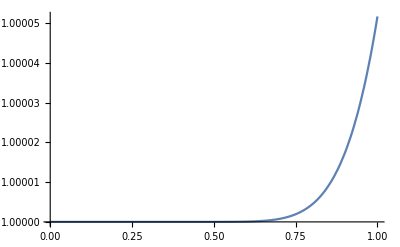

```mathematica
Plot[Cosh[π^2/(2 h)]/(1/2 Exp[π^2/(2 h)]),{h,0.001,1},PlotRange->All]
```

```mathematica
Integrate[Tan[I π/h z],{z,-y,y},Assumptions->{n>0,h>0,y>0,n>1}]
```

0

```mathematica
Integrate[Tan[π n +I π/h z],{z,-y,y},Assumptions->{n>0,h>0,y>0,n>1, Cos[n π]<0}]
```

(ⅈ h (-Log[Cos[π (n-(ⅈ y)/h)]]+Log[Cos[π (n+(ⅈ y)/h)]]))/π

```mathematica
%32-%33
```

0

```mathematica
TeXForm[(-Log[Cos[π (n-(ⅈ y)/h)]]+Log[Cos[π (n+(ⅈ y)/h)]])]
```

\log \left(\cos \left(\pi  \left(n+\frac{i y}{h}\right)\right)\right)-\log \left(\cos
   \left(\pi  \left(n-\frac{i y}{h}\right)\right)\right)

```mathematica
Simplify[(-Log[Cos[π (n-(ⅈ y)/h)]]+Log[Cos[π (n+(ⅈ y)/h)]]),Assumptions->{Element[n,Integers]}]
```

-Log[Cos[π (n-(ⅈ y)/h)]]+Log[Cos[π (n+(ⅈ y)/h)]]

```mathematica
Plot3D[Im[ψ[z]/.z-> x+I y],{x,-20,20},{y,-π/3,π/3}]
```

-Graphics3D-

```mathematica
ψ[z_]  = z Tanh[π/2 Sinh[z]]
```

z Tanh[1/2 π Sinh[z]]

```mathematica
ψ'[z]/.z-> x+I y
```

1/2 π (x+ⅈ y) Cosh[x+ⅈ y] Sech[1/2 π Sinh[x+ⅈ y]]^2+Tanh[1/2 π Sinh[x+ⅈ y]]

```mathematica
Integrate[(π/h)^(3/2)Sin[π/h(x+I y)- (π ν)/2- π/4](x+I y)^(1/2)Exp[- λ π/h(x+I y)],{y,-z,z}, Assumptions->{x>0,ν>0,λ>0,z>0,σ>0,n>0}]
Simplify[%151/.x-> h (n+ ν/2+1/4), Assumptions->{h>0,n>0,λ>0,z>0}]
```

(-1/4-ⅈ/4) ⅇ^(-(π x λ)/h) √(1/h) √(π/2) ((2 ⅇ^(-(ⅈ π (-2 x+2 z (-ⅈ+λ)+h ν))/(2 h)) √(x+ⅈ z))/(-1-ⅈ λ)-(2 ⅈ ⅇ^((π (2 ⅈ x+2 z+2 ⅈ z λ-ⅈ h ν))/(2 h)) √(x-ⅈ z))/(-ⅈ+λ)-(2 ⅇ^((ⅈ π (-2 x+2 z (ⅈ+λ)+h ν))/(2 h)) √(x-ⅈ z))/(ⅈ+λ)+(2 ⅇ^(-(ⅈ π (2 x+2 z (ⅈ+λ)-h ν))/(2 h)) √(x+ⅈ z))/(ⅈ+λ)+(ⅈ ⅇ^((π x λ)/h-(ⅈ π ν)/2) √h Erf[(√π √(x-ⅈ z) √(-ⅈ+λ))/(√h)])/(-ⅈ+λ)^(3/2)-(ⅈ ⅇ^((π x λ)/h-(ⅈ π ν)/2) √h Erf[(√π √(x+ⅈ z) √(-ⅈ+λ))/(√h)])/(-ⅈ+λ)^(3/2)+(ⅇ^((π x λ)/h+(ⅈ π ν)/2) √h Erf[(√π √(x-ⅈ z) √(ⅈ+λ))/(√h)])/(ⅈ+λ)^(3/2)-(ⅇ^((π x λ)/h+(ⅈ π ν)/2) √h Erf[(√π √(x+ⅈ z) √(ⅈ+λ))/(√h)])/(ⅈ+λ)^(3/2))

1/(24 √h)ⅇ^(-(1/4+n) π) √π Abs[(1+ⅈ) ⅇ^((ⅈ π (3 h+12 h n+(4+4 ⅈ) π))/(12 h)) √(9 h+36 h n-12 ⅈ π)-(1+ⅈ) ⅇ^((π (9 ⅈ h (1+4 n)+(4+4 ⅈ) π))/(12 h)) √(9 h+36 h n-12 ⅈ π)-(1+ⅈ) ⅇ^((ⅈ (3 h+12 h n-(4+4 ⅈ) π) π)/(12 h)) √(9 h+36 h n+12 ⅈ π)+(1+ⅈ) ⅇ^((ⅈ (9 h+36 h n-(4-4 ⅈ) π) π)/(12 h)) √(9 h+36 h n+12 ⅈ π)-3 ⅇ^(π/4+(1+2 ⅈ) n π) √((1-ⅈ) h) Erf[1/2 √((1-ⅈ) π) √(1+4 n-(4 ⅈ π)/(3 h))]-3 ⅈ ⅇ^(π/4+(1+2 ⅈ) n π) √((1+ⅈ) h) Erf[1/2 √((1+ⅈ) π) √(1+4 n-(4 ⅈ π)/(3 h))]+3 ⅇ^(π/4+(1+2 ⅈ) n π) √((1-ⅈ) h) Erf[1/2 √((1-ⅈ) π) √(1+4 n+(4 ⅈ π)/(3 h))]+3 ⅈ ⅇ^(π/4+(1+2 ⅈ) n π) √((1+ⅈ) h) Erf[1/2 √((1+ⅈ) π) √(1+4 n+(4 ⅈ π)/(3 h))]]

```mathematica
(((-1/4-ⅈ/4) ⅇ^(-(π x λ)/h) √(1/h) √(π/2) ((2 ⅇ^(-(ⅈ π (-2 x+2 z (-ⅈ+λ)+h ν))/(2 h)) √(x+ⅈ z))/(-1-ⅈ λ)-(2 ⅈ ⅇ^((π (2 ⅈ x+2 z+2 ⅈ z λ-ⅈ h ν))/(2 h)) √(x-ⅈ z))/(-ⅈ+λ)-(2 ⅇ^((ⅈ π (-2 x+2 z (ⅈ+λ)+h ν))/(2 h)) √(x-ⅈ z))/(ⅈ+λ)+(2 ⅇ^(-(ⅈ π (2 x+2 z (ⅈ+λ)-h ν))/(2 h)) √(x+ⅈ z))/(ⅈ+λ)+(ⅈ ⅇ^((π x λ)/h-(ⅈ π ν)/2) √h Erf[(√π √(x-ⅈ z) √(-ⅈ+λ))/(√h)])/(-ⅈ+λ)^(3/2)-(ⅈ ⅇ^((π x λ)/h-(ⅈ π ν)/2) √h Erf[(√π √(x+ⅈ z) √(-ⅈ+λ))/(√h)])/(-ⅈ+λ)^(3/2)+(ⅇ^((π x λ)/h+(ⅈ π ν)/2) √h Erf[(√π √(x-ⅈ z) √(ⅈ+λ))/(√h)])/(ⅈ+λ)^(3/2)-(ⅇ^((π x λ)/h+(ⅈ π ν)/2) √h Erf[(√π √(x+ⅈ z) √(ⅈ+λ))/(√h)])/(ⅈ+λ)^(3/2)))/.x-> h (n+ν/2+1/4)/.ν-> 0)/.λ-> 0.1/.z->100 h π
```

(-1/4-ⅈ/4) ⅇ^(-0.314159 (1/4+n)) √(1/h) √(π/2) ((-0.19802+1.9802 ⅈ) ⅇ^((ⅈ ((62.8319+628.319 ⅈ) h-2 h (1/4+n)) π)/(2 h)) √(h (1/4+n)-100 ⅈ h π)+(1.9802-0.19802 ⅈ) ⅇ^((((628.319+62.8319 ⅈ) h+2 ⅈ h (1/4+n)) π)/(2 h)) √(h (1/4+n)-100 ⅈ h π)-(1.9802-0.19802 ⅈ) ⅇ^(-(ⅈ ((62.8319-628.319 ⅈ) h-2 h (1/4+n)) π)/(2 h)) √(h (1/4+n)+100 ⅈ h π)+(0.19802-1.9802 ⅈ) ⅇ^(-(ⅈ ((62.8319+628.319 ⅈ) h+2 h (1/4+n)) π)/(2 h)) √(h (1/4+n)+100 ⅈ h π)-(0.589482+0.798559 ⅈ) ⅇ^(0.314159 (1/4+n)) √h Erf[((1.31746+1.19229 ⅈ) √(h (1/4+n)-100 ⅈ h π))/(√h)]+(0.589482+0.798559 ⅈ) ⅇ^(0.314159 (1/4+n)) √h Erf[((1.31746+1.19229 ⅈ) √(h (1/4+n)+100 ⅈ h π))/(√h)]-(0.589482-0.798559 ⅈ) ⅇ^(0.314159 (1/4+n)) √h Erfi[((1.19229+1.31746 ⅈ) √(h (1/4+n)-100 ⅈ h π))/(√h)]+(0.589482-0.798559 ⅈ) ⅇ^(0.314159 (1/4+n)) √h Erfi[((1.19229+1.31746 ⅈ) √(h (1/4+n)+100 ⅈ h π))/(√h)])

```mathematica
Plot3D[Log10[Abs[%176]],{h,0.005,0.01},{n,10,500}]
```

-Graphics3D-

```mathematica
Integrate[(π/h)^(3/2)Exp[I π/h(x+I y)- (π ν)/2- π/4](x+I y)^(1/2)Exp[-  λ π/h(x+I y)^2],{y,-z,z}, Assumptions->{x>0,ν>0,λ>0,z>0,σ>0,n>0}]
Simplify[%187/.x-> h (n+ ν/2+1/4), Assumptions->{h>0,n>0,λ>0,z>0}]
```

Integrate[ⅇ^(-π/4+(ⅈ π (x+ⅈ y))/h-(π (x+ⅈ y)^2 λ)/h-(π ν)/2) (1/h)^(3/2) π^(3/2) √(x+ⅈ y),{y,-z,z},Assumptions→{x>0,ν>0,λ>0,z>0,σ>0,n>0}]

$Aborted

```mathematica
Integrate[(π/h)^(3/2)Exp[I π/h(x+I y)- (π ν)/2- π/4](x+I y)^(1/2)Exp[-  λ π/h(x+I y)],{y,-z,z}, Assumptions->{x>0,ν>0,λ>0,z>0,σ>0,n>0}]
```

1/(2 (-ⅈ+λ)^(3/2))ⅈ ⅇ^(-(π (4 (z+3 x λ+ⅈ z λ)+h (3+6 ν)))/(4 h)) √(1/h) √π (2 ⅇ^((π (h+2 ⅈ x+4 x λ+2 h ν))/(2 h)) (-ⅇ^((2 π z (1+ⅈ λ))/h) √(x-ⅈ z)+√(x+ⅈ z)) √(-ⅈ+λ)+ⅇ^((π (h+2 z+6 x λ+2 ⅈ z λ+2 h ν))/(2 h)) √h Erf[(√π √(x-ⅈ z) √(-ⅈ+λ))/(√h)]-ⅇ^((π (h+2 z+6 x λ+2 ⅈ z λ+2 h ν))/(2 h)) √h Erf[(√π √(x+ⅈ z) √(-ⅈ+λ))/(√h)])

```mathematica
Abs[%189/.x-> h(n+ν/2+1/4)/.z-> π/3/.λ-> 1]
```

1/(2 2^(3/4))ⅇ^(-1/4 π Re[(4 ((1/3+ⅈ/3) π+3 h (1/4+n+ν/2))+h (3+6 ν))/h]) √π Abs[√(1/h) (2 √(1-ⅈ) ⅇ^((π (h+(4+2 ⅈ) h (1/4+n+ν/2)+2 h ν))/(2 h)) (-ⅇ^(((2/3+(2 ⅈ)/3) π^2)/h) √(-(ⅈ π)/3+h (1/4+n+ν/2))+√((ⅈ π)/3+h (1/4+n+ν/2)))+ⅇ^((π (h+(2/3+(2 ⅈ)/3) π+6 h (1/4+n+ν/2)+2 h ν))/(2 h)) √h Erf[(√((1-ⅈ) π) √(-(ⅈ π)/3+h (1/4+n+ν/2)))/(√h)]-ⅇ^((π (h+(2/3+(2 ⅈ)/3) π+6 h (1/4+n+ν/2)+2 h ν))/(2 h)) √h Erf[(√((1-ⅈ) π) √((ⅈ π)/3+h (1/4+n+ν/2)))/(√h)])]

```mathematica
nvals = {}
yvals={}
For[i = 70, i≤ 100, i++, AppendTo[nvals,i];AppendTo[yvals,Abs[%95/.λ-> 0.1/.h-> 0.1/.z-> π/3/.ν-> 0/.n-> i]]]
```

{}

{}

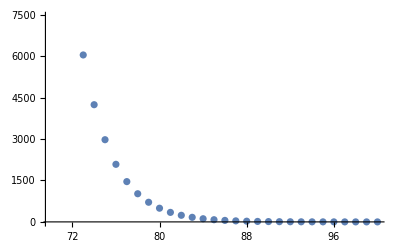

```mathematica
data=Transpose@{nvals,yvals};
ListPlot[data]
```

```mathematica
Integrate[(π/h)^(3/2)Exp[I π/h(x+I y)](x+I y)^(1/2)Exp[-π^2/(4 σ^2 h^2)(x+I y)^2],{y,-z,z}, Assumptions->{x>0,ν>0,λ>0,z>0,σ>0,n>0}]
```

$Aborted

```mathematica
Plot[Abs[BesselY[0,π/0.01(0.01*200000+I y)]],{y,-π/10,π/10}]
```

-Graphics-

```mathematica
Plot3D[Abs[HankelH1[0,x+I y]HeavisideTheta[y]+HankelH2[0,x+I y]HeavisideTheta[-y]],{x,-10,10},{y,-100,100},PlotRange->All]
```

```mathematica
Normal@Series[HankelH1[0,x+I y]HeavisideTheta[y]+HankelH2[0,x+I y]HeavisideTheta[-y],{y,0,2}]
```

(HankelH2[0,x]-ⅈ y HankelH2[1,x]+1/4 y^2 (HankelH2[0,x]-HankelH2[2,x])) HeavisideTheta[-y]+(HankelH1[0,x]-ⅈ y HankelH1[1,x]+1/4 y^2 (HankelH1[0,x]-HankelH1[2,x])) HeavisideTheta[y]